```mathematica
π//N
```

3.14159

```mathematica
N[π,50]
```

3.1415926535897932384626433832795028841971693993751

```mathematica
N[E,26]
```

2.7182818284590452353602875

```mathematica
Sqrt[968]
```

22 √2

```mathematica
%//N
```

31.1127

```mathematica
a=3;
b2xy=4;
xyz5=5;
```

```mathematica
?`*
```

```mathematica
Remove["`*"]
```

```mathematica
?`*
```

Information::nomatch: No symbol matching "`*" found.

```mathematica
Factor[x^3-6 x^2+11x-6]
```

(-3+x) (-2+x) (-1+x)

```mathematica
Solve[x^3-2x+1==0]
```

{{x→1},{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

```mathematica
Expand[(x+1)^10]
```

1+10 x+45 x^2+120 x^3+210 x^4+252 x^5+210 x^6+120 x^7+45 x^8+10 x^9+x^10

```mathematica
%//TraditionalForm
```

x^10+10 x^9+45 x^8+120 x^7+210 x^6+252 x^5+210 x^4+120 x^3+45 x^2+10 x+1

```mathematica
Factor[%]
```

(1+x)^10

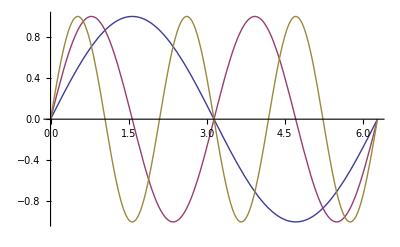

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2π}]
```

```mathematica
Plot3D[(x^2+3 y^2)E^(-(x^2+y^2)),{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
90Degree//N
```

1.5708

```mathematica
90Degree
```

90 °

```mathematica
Solve[x^2-x-1==0]
```

```mathematica
{{x->1/2 (1-√5)},{x->1/2 (1+√5)}}
%//N
```

{{x→1/2 (1-√5)},{x→1/2 (1+√5)}}

{{x→-0.618034},{x→1.61803}}

```mathematica
GoldenRatio//N
```

1.61803

```mathematica
Log[100]
```

Log[100]

```mathematica
Log10[100]
```

2

```mathematica
Log[2,100]
```

Log[100]/Log[2]

```mathematica
%//N
```

6.64386

```mathematica
Sin[60°]
```

(√3)/2

```mathematica
ArcSin[1]
```

π/2

```mathematica
ArcCos[Cos[3π]]
```

π

```mathematica
f[0]=1;
f[n_]:=n f[n-1]
```

```mathematica
f[5]
```

120

```mathematica
f[10]
```

3628800

```mathematica
g[x_]:=x^2/;x≥0
g[x_]:=-x^2/;x<0
g[3]
```

9

```mathematica
g[-3]
```

-9

```mathematica
F[x_]:=∫_0^x t Exp[t]Sin[t]ⅆt
```

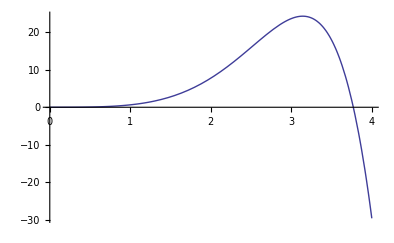
{57.544,-Graphics-}

```mathematica
Plot[F[x],{x,0,4}]//Timing
```

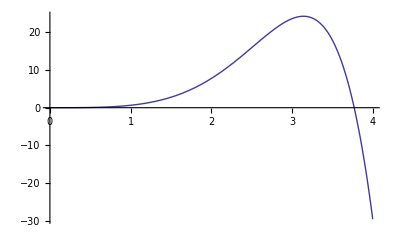
{57.891,-Graphics-}

```mathematica
F[x_]:=∫_0^x t Exp[t]Sin[t]ⅆt;
Plot[F[x],{x,0,4}]//Timing
```

```mathematica
Clear[x]
```

```mathematica
x^2+5 x+6/.x->3
```

30

```mathematica
a=Expand[(x+1)^3]
```

1+3 x+3 x^2+x^3

```mathematica
a=Factor[poly];
b:=Factor[poly];
poly=x^2+2x+1;
a
```

1+2 x+x^2

```mathematica
b
```

(1+x)^2

```mathematica
Sum[i^2,{i,1,20}]
```

2870

```mathematica
Sum[1/i,{i,15,51,2}]
```

63501391475806044193/96845140757687397075

```mathematica
%//N
```

0.6557

```mathematica
Sum[1/i^2,{i,1,Infinity}]
```

π^2/6

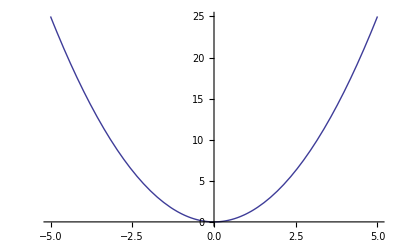

```mathematica
Plot[x^2,{x,-5,5}]
```

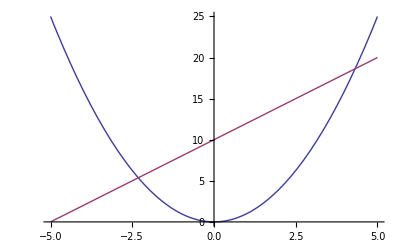

```mathematica
Plot[{x^2,2x+10},{x,-5,5}]
```

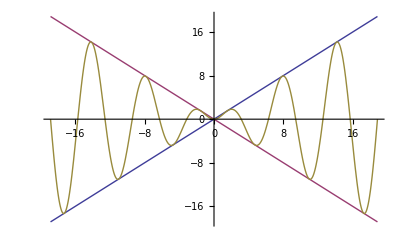

```mathematica
Plot[{x,-x,x Sin[x]},{x,-6π,6π}]
```

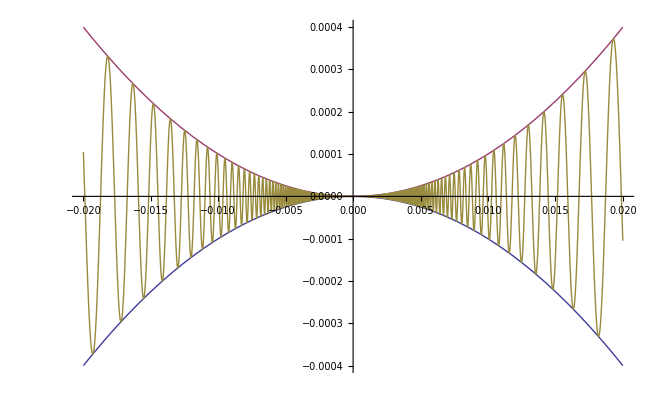

```mathematica
Plot[{-x^2,x^2,x^2 Sin[1/x]},{x,-0.02,0.02}]
```

```mathematica
f[x_]:=x^2/;x≤2
f[x_]:=8-2x/;x>2
```

```mathematica
f[-4]
```

16

```mathematica
f[4]
```

0

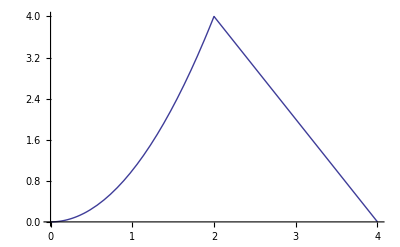

```mathematica
Plot[f[x],{x,0,4}]
```

```mathematica
f[x_,y_]=x^2+y^3
```

x^2+y^3

```mathematica
f[2,3]
```

31

```mathematica
f[3,2]
```

17

```mathematica
f[x_]:=√x
```

```mathematica
g[x_]:=x^2+2x+3
```

```mathematica
h1[x_]:=f[x]+g[x]
```

```mathematica
h1
```

h1

```mathematica
h1[x]
```

3+√x+2 x+x^2

```mathematica
h2[x_]=f[x]-g[x]
```

-3+√x-2 x-x^2

```mathematica
h3[x_]=f[x]g[x]
```

√x (3+2 x+x^2)

```mathematica
h4[x_]=f[x]/g[x]
```

(√x)/(3+2 x+x^2)

```mathematica
h5[x_]=f[g[x]]
```

√(3+2 x+x^2)

```mathematica
list={1,2,3,4,5};
Total[list]
```

15

```mathematica
Accumulate[list]
```

{1,3,6,10,15}

```mathematica
Max[list]
```

5

```mathematica
Min[list]
```

1

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[i,{i,2,8,0.5}]
```

{2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.}

```mathematica
Range[1,25,5]
```

{1,6,11,16,21}

```mathematica
p[x_]:=x^2-8x+10;
```

```mathematica
Array[p,10,2]
```

{-2,-5,-6,-5,-2,3,10,19,30,43}

```mathematica
p[Range[2,11,1]]
```

{-2,-5,-6,-5,-2,3,10,19,30,43}

```mathematica
Range[0,2π,π/6]
```

{0,π/6,π/3,π/2,(2 π)/3,(5 π)/6,π,(7 π)/6,(4 π)/3,(3 π)/2,(5 π)/3,(11 π)/6,2 π}

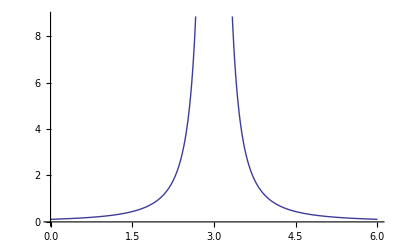

```mathematica
Clear[f]
f[x_]:=1/(x-3)^2/;x<2.9 ||x>3.1
f[x_]:=100/;2.9≤x≤3.1
Plot[f[x],{x,0,6}]
```

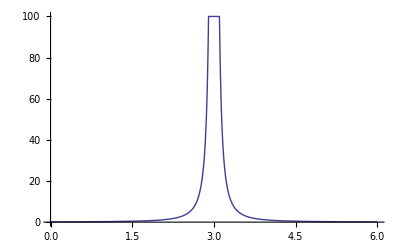

```mathematica
Plot[f[x],{x,0,6},PlotRange->All]
```

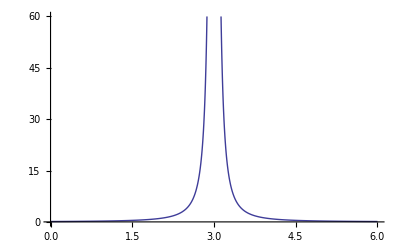

```mathematica
Plot[f[x],{x,0,6},PlotRange->{0,60}]
```

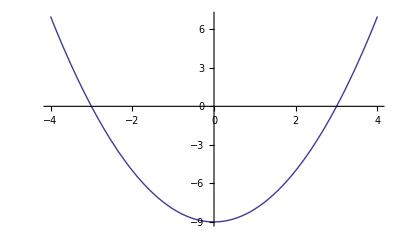

```mathematica
g1=Plot[x^2-9,{x,-4,4}]
```

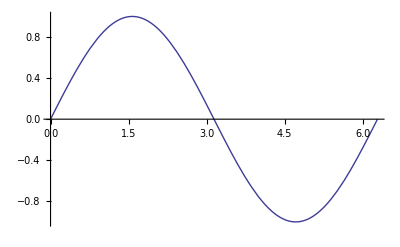

```mathematica
g2=Plot[Sin[x],{x,0,2π}]
```

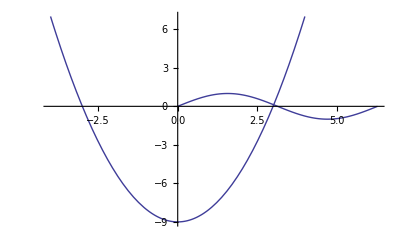

```mathematica
Show[g1,g2,PlotRange->All]
```

```mathematica
??Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

Attributes[Plot]={HoldAll,Protected,ReadProtected}
 
Options[Plot]={AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
Clear["`*"]
```

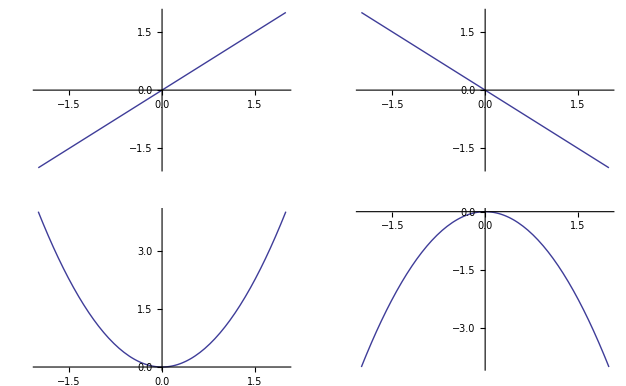

```mathematica
g1=Plot[x,{x,-2,2}];
g2=Plot[-x,{x,-2,2}];
g3=Plot[x^2,{x,-2,2}];
g4=Plot[-x^2,{x,-2,2}];
GraphicsGrid[{{g1,g2},{g3,g4}}]
```

```mathematica
??GraphicsGrid
```

GraphicsGrid[{{g_11,g_12,…},…}] generates a graphic in which the g_ij are laid out in a two-dimensional grid.

Attributes[GraphicsGrid]={Protected,ReadProtected}
 
Options[GraphicsGrid]={Alignment→{Center,Center},AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DefaultBaseStyle→GraphicsGrid,DisplayFunction:>$DisplayFunction,Dividers→None,Epilog→{},FormatType:>TraditionalForm,Frame→None,FrameLabel→None,FrameStyle→Automatic,FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,BoxForm`ItemAspectRatio→Automatic,LabelStyle→{},Method→Automatic,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Spacings→Scaled[0.1],Ticks→Automatic,TicksStyle→{}}

```mathematica
Plot[x^2,{x,-5,5}]
```

-Graphics-

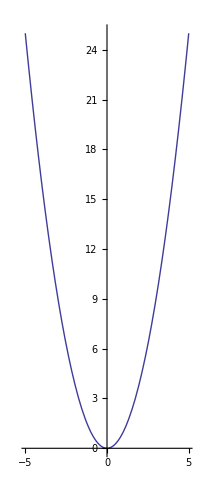

```mathematica
Plot[x^2,{x,-5,5},AspectRatio->Automatic]
```

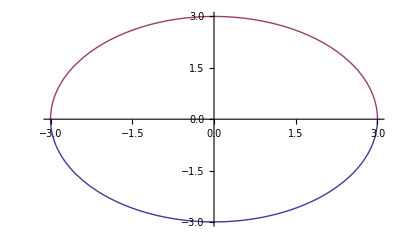

```mathematica
Plot[{-Sqrt[9-x^2],Sqrt[9-x^2]},{x,-3,3}]
```

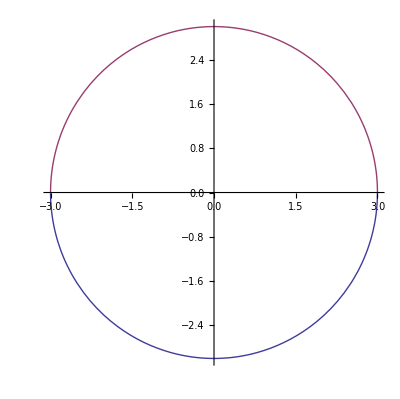

```mathematica
Plot[{-Sqrt[9-x^2],Sqrt[9-x^2]},{x,-3,3},AspectRatio->Automatic]
```